0.000236308+1.75588×10^-9 x

1.15287×10^-6+1.33212×10^-13 x

7.20374×10^-7+2.42704×10^-13 x-6.58073×10^-20 x^2+1.16759×10^-26 x^3-1.10283×10^-33 x^4+4.15462×10^-41 x^5

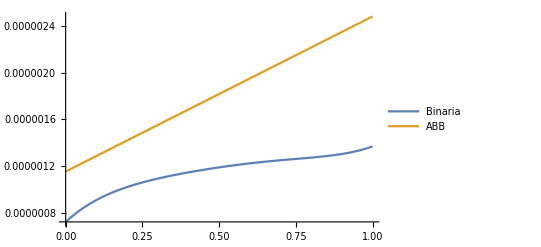

```mathematica
lineal=Fit[{{100,8.70228*10^-7},{1000,2.77758*10^-6},{5000,1.56999*10^-5},{10000,2.10762*10^-5},{50000,0.000100839},{100000,0.000190556},{200000,0.000375354},{400000,0.000731313},{600000,0.001224697},{800000,0.002665651},{1000000,0.001823199},{2000000,0.003687847},{3000000,0.006287658},{4000000,0.007306921},{5000000,0.009912563},{6000000,0.011102915},{7000000,0.012512947},{8000000,0.014274967},{9000000,0.015519405},{10000000,0.017345857}},{1,x},x]
ABB=Fit[{{100,6.4373*10^-7},{1000,6.07967*10^-7},{5000,5.96046*10^-7},{10000,7.03335*10^-7},{50000,9.53674*10^-7},{100000,7.39098*10^-7},{200000,1.20401*10^-6},{400000,3.92199*10^-6},{600000,1.12057*10^-6},{800000,1.19209*10^-6},{1000000,1.50204*10^-6},{2000000,1.50204*10^-6},{3000000,1.58548*10^-6},{4000000,1.692775*10^-6},{5000000,1.63317*10^-6},{6000000,2.12193*10^-6},{7000000,1.85966*10^-6},{8000000,1.83582*10^-6},{9000000,3.42131*10^-6},{10000000,1.83582*10^-6}},{1,x},x]
binaria=Fit[{{100,6.67572*10^-7},{1000,7.51019*10^-7},{5000,6.55651*10^-7},{10000,5.96046*10^-7},{50000,8.46386*10^-7},{100000,7.98702*10^-7},{200000,9.05991*10^-7},{400000,8.46386*10^-7},{600000,7.39098*10^-7},{800000,9.41753*10^-7},{1000000,7.15256*10^-7},{2000000,1.15633*10^-6},{3000000,1.09673*10^-6},{4000000,1.13249*10^-6},{5000000,1.10865*10^-6},{6000000,1.26362*10^-6},{7000000,1.27554*10^-6},{8000000,1.28746*10^-6},{9000000,1.26362*10^-6},{10000000,1.38283*10^-6}},{1,x,x^2,x^3,x^4,x^5},x]

g1=Plot[{binaria,ABB},{x,0,10000000},PlotLegends->{"Binaria","ABB"}]
```

0.0000858628+1.46546×10^-9 x

0.0000211462+6.03491×10^-12 x-5.65412×10^-18 x^2+1.76786×10^-24 x^3-2.1856×10^-31 x^4+9.28242×10^-39 x^5

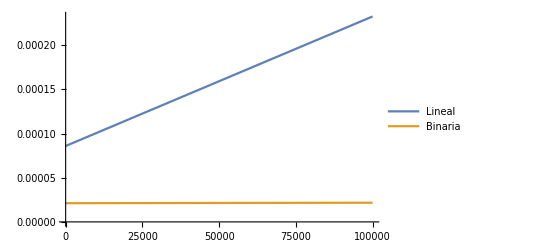

```mathematica
linealhilos=Fit[{{100,1.91808*10^-5},{1000,2.19584*10^-5},{5000,3.016*10^-5},{10000,4.41432*10^-5},{50000,0.00011034},{100000,0.000185752},{200000,0.000329947},{400000,0.000737524},{600000,0.000922275},{800000,0.001324618},{1000000,0.001581335},{2000000,0.003110409},{3000000,0.004633558},{4000000,0.006227768},{5000000,0.007418943},{6000000,0.008559358},{7000000,0.010078263},{8000000,0.012636209},{9000000,0.013014209},{10000000,0.01450572}},{1,x},x]

binariahilos=Fit[{{100,2.03848*10^-5},{1000,2.32577*10^-5},{5000,1.89662*10^-5},{10000,1.98126*10^-5},{50000,1.94073*10^-5},{100000,2.53797*10^-5},{200000,2.23756*10^-5},{400000,2.3675*10^-5},{600000,2.48075*10^-5},{800000,2.27451*10^-5},{1000000,2.07186*10^-5},{2000000,2.22445*10^-5},{3000000,2.05636*10^-5},{4000000,2.06113*10^-5},{5000000,2.43545*10^-5},{6000000,2.54989*10^-5},{7000000,2.23875*10^-5},{8000000,2.17199*10^-5},{9000000,2.10524*10^-5},{10000000,2.63453*10^-5}},{1,x,x^2,x^3,x^4,x^5},x]

g2=Plot[{linealhilos,binariahilos},{x,0,100000},PlotLegends->{"Lineal","Binaria"}]
```